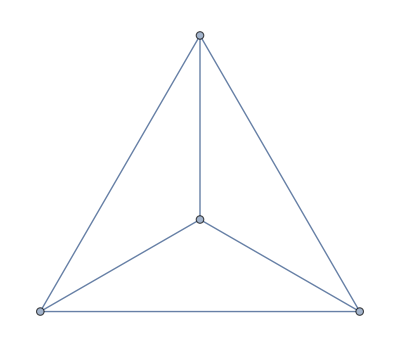

```mathematica
CompleteGraph[4]
```

```mathematica
6 x^5+5 x^4-12 x^3-5 x^2+6x
```

6 x-5 x^2-12 x^3+5 x^4+6 x^5

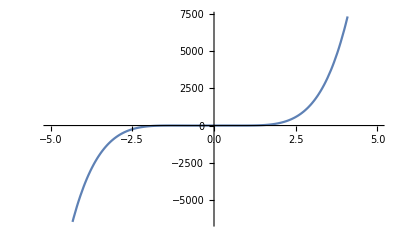

```mathematica
Plot[6 x-5 x^2-12 x^3+5 x^4+6 x^5,{x,-5.,5.}]
```

```mathematica
(6 x-5 x^2-12 x^3+5 x^4+6 x^5)/x
```

(6 x-5 x^2-12 x^3+5 x^4+6 x^5)/x

```mathematica
Simplify[(6 x-5 x^2-12 x^3+5 x^4+6 x^5)/x]
```

6-5 x-12 x^2+5 x^3+6 x^4

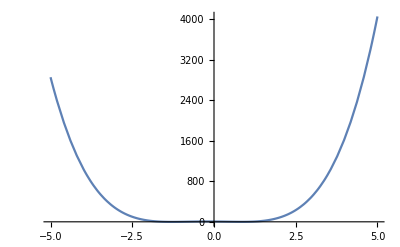

```mathematica
Plot[6-5 x-12 x^2+5 x^3+6 x^4,{x,-5.,5.}]
```

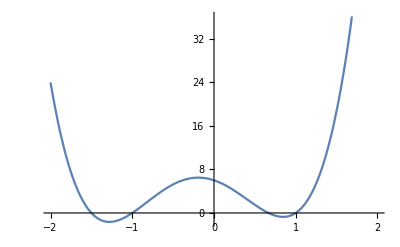

```mathematica
Plot[6-5 x-12 x^2+5 x^3+6 x^4,{x,-2,2}]
```

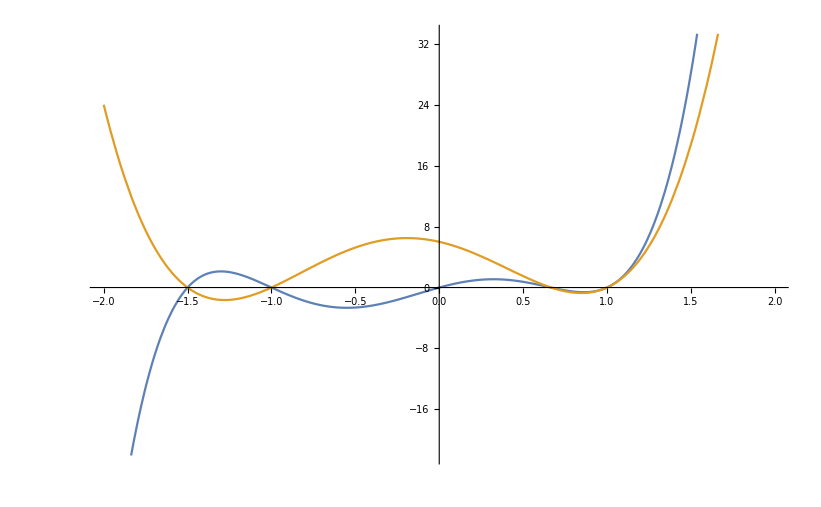

```mathematica
Plot[{6 x-5 x^2-12 x^3+5 x^4+6 x^5,6-5 x-12 x^2+5 x^3+6 x^4},{x,-2,2}]
```

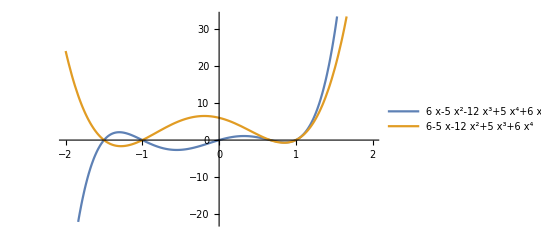

```mathematica
Plot[{6 x-5 x^2-12 x^3+5 x^4+6 x^5,6-5 x-12 x^2+5 x^3+6 x^4},{x,-2,2},PlotLegends->"Expressions"]
```

```mathematica
Plot[{6 x-5 x^2-12 x^3+5 x^4+6 x^5,6-5 x-12 x^2+5 x^3+6 x^4},{x,-2,2},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Map[ArcCurvature[{x,#},x]&,{6 x-5 x^2-12 x^3+5 x^4+6 x^5,6-5 x-12 x^2+5 x^3+6 x^4}]
```

{(2 Abs[-5-36 x+30 x^2+60 x^3])/((37-120 x-332 x^2+960 x^3+1256 x^4-2040 x^5-1760 x^6+1200 x^7+900 x^8)^(3/2)),(6 Abs[-4+5 x+12 x^2])/((26+240 x+426 x^2-960 x^3-927 x^4+720 x^5+576 x^6)^(3/2))}

```mathematica
FullSimplify[Map[ArcCurvature[{x,#},x]&,{6 x-5 x^2-12 x^3+5 x^4+6 x^5,6-5 x-12 x^2+5 x^3+6 x^4}],x∈Reals]
```

{(2 Abs[5-6 x (-6+5 x (1+2 x))])/(37+4 x (-5+x (-18+5 x (2+3 x))) (6+x (-5+x (-18+5 x (2+3 x)))))^(3/2),(6 Abs[-4+x (5+12 x)])/(26+3 x (-8+x (5+8 x)) (-10+3 x (-8+x (5+8 x))))^(3/2)}

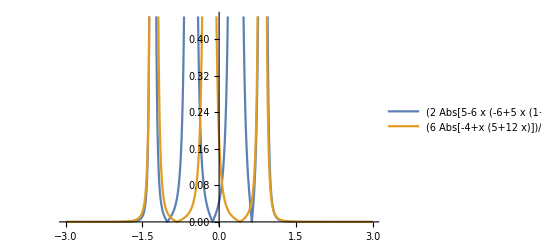

```mathematica
Plot[
{(2 Abs[5-6 x (-6+5 x (1+2 x))])/(37+4 x (-5+x (-18+5 x (2+3 x))) (6+x (-5+x (-18+5 x (2+3 x)))))^(3/2),(6 Abs[-4+x (5+12 x)])/(26+3 x (-8+x (5+8 x)) (-10+3 x (-8+x (5+8 x))))^(3/2)}
,{x,-3,3}
,PlotLegends->"Expressions"]
```

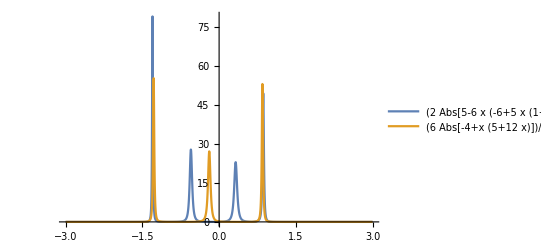

```mathematica
Plot[
{(2 Abs[5-6 x (-6+5 x (1+2 x))])/(37+4 x (-5+x (-18+5 x (2+3 x))) (6+x (-5+x (-18+5 x (2+3 x)))))^(3/2),(6 Abs[-4+x (5+12 x)])/(26+3 x (-8+x (5+8 x)) (-10+3 x (-8+x (5+8 x))))^(3/2)}
,{x,-3,3}
,PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
Abs[f[x]]/f[x]
```

Abs[f[x]]/f[x]

```mathematica
FullSimplify[Abs[f[x]]/f[x]]
```

1/Sign[f[x]]

```mathematica
Limit[
Integrate[{(2 Abs[5-6 x (-6+5 x (1+2 x))])/(37+4 x (-5+x (-18+5 x (2+3 x))) (6+x (-5+x (-18+5 x (2+3 x)))))^(3/2),(6 Abs[-4+x (5+12 x)])/(26+3 x (-8+x (5+8 x)) (-10+3 x (-8+x (5+8 x))))^(3/2)},{x,-a,a}]
,a->∞]
```

$Aborted

```mathematica
Limit[
NIntegrate[{(2 Abs[5-6 x (-6+5 x (1+2 x))])/(37+4 x (-5+x (-18+5 x (2+3 x))) (6+x (-5+x (-18+5 x (2+3 x)))))^(3/2),(6 Abs[-4+x (5+12 x)])/(26+3 x (-8+x (5+8 x)) (-10+3 x (-8+x (5+8 x))))^(3/2)},{x,-a,a}]
,a->∞]
```

NIntegrate::nlim: x = -1. a is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

$Aborted

```mathematica
Limit[
NIntegrate[(6 Abs[-4+x (5+12 x)])/(26+3 x (-8+x (5+8 x)) (-10+3 x (-8+x (5+8 x))))^(3/2),{x,-a,a}]
,a->∞]
```

NIntegrate::nlim: x = -1. a is not a valid limit of integration.

$Aborted

```mathematica
Manipulate[
NIntegrate[(6 Abs[-4+x (5+12 x)])/(26+3 x (-8+x (5+8 x)) (-10+3 x (-8+x (5+8 x))))^(3/2),{x,-a,a}]
,{a,0,1000}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.291530511912676038033254144465900026261806488037109375}. NIntegrate obtained 3.98838 and 0.0176615 for the integral and error estimates.

```mathematica
Manipulate[
NIntegrate[(6 Abs[-4+x (5+12 x)])/(26+3 x (-8+x (5+8 x)) (-10+3 x (-8+x (5+8 x))))^(3/2),{x,-a,a}]
,{a,0,10000}]
```

```mathematica
(2 Abs[5-6 x (-6+5 x (1+2 x))])/(37+4 x (-5+x (-18+5 x (2+3 x))) (6+x (-5+x (-18+5 x (2+3 x)))))^(3/2)
```

(2 Abs[5-6 x (-6+5 x (1+2 x))])/(37+4 x (-5+x (-18+5 x (2+3 x))) (6+x (-5+x (-18+5 x (2+3 x)))))^(3/2)

```mathematica
Manipulate[
NIntegrate[(2 Abs[5-6 x (-6+5 x (1+2 x))])/(37+4 x (-5+x (-18+5 x (2+3 x))) (6+x (-5+x (-18+5 x (2+3 x)))))^(3/2),{x,-a,a}]
,{a,0,10000}]
```

```mathematica
FullSimplify[ArcCurvature[{x,(x^3-x)/x^a},x],x∈Reals∧a∈]
```

√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3))

```mathematica
Manipulate[
Plot[
√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3))
,{x,-2,2}
,PlotLegends->"Expressions",PlotRange->Full]
,{a,0,10}]
```

```mathematica
FullSimplify[ArcCurvature[{x,x^a(x^3-x)},x],x∈Reals∧a∈]
```

√((x^(-2+2 a) (a (1+a)-(2+a) (3+a) x^2)^2)/((1+x^(2 a) (1+a-(3+a) x^2)^2)^3))

```mathematica
Manipulate[
Plot[
{√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),√((x^(-2+2 b) (b (1+b)-(2+b) (3+b) x^2)^2)/((1+x^(2 b) (1+b-(3+b) x^2)^2)^3))}
,{x,-2,2}
,PlotLegends->"Expressions",PlotRange->Full]
,{a,0,10},{b,0,10}]
```

```mathematica
FullSimplify[ArcCurvature[{x,x^b(x^3-x)},x],x∈Reals∧a∈]
```

√((x^(-2+2 b) (b (1+b)-(2+b) (3+b) x^2)^2)/((1+x^(2 b) (1+b-(3+b) x^2)^2)^3))

```mathematica
Manipulate[
Plot[
{√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),√((x^(-2+2 b) (b (1+b)-(2+b) (3+b) x^2)^2)/((1+x^(2 b) (1+b-(3+b) x^2)^2)^3))}
,{x,-2,2}
,PlotLegends->"Expressions",PlotRange->{0,10},ImageSize->Large]
,{a,0,10},{b,0,10}]
```

```mathematica
Manipulate[
Plot[
{√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),√((x^(-2+2 b) (b (1+b)-(2+b) (3+b) x^2)^2)/((1+x^(2 b) (1+b-(3+b) x^2)^2)^3))}
,{x,-2,2}
,PlotLegends->"Expressions",PlotRange->{0,10},ImageSize->Large]
,{a,0,10,1},{b,0,10,1}]
```

```mathematica
Manipulate[
Plot[
{√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),√((x^(-2+2 b) (b (1+b)-(2+b) (3+b) x^2)^2)/((1+x^(2 b) (1+b-(3+b) x^2)^2)^3))}
,{x,-2,2}
,PlotLegends->{f[x]/x,x f[x]},PlotRange->{0,10},ImageSize->Large]
,{a,0,10,1},{b,0,10,1}]
```